```mathematica
v1Color=Blue;
```

```mathematica
v2mColor=Purple;
```

```mathematica
(***************************************)
```

```mathematica
dateMouseSessionListV1={{"030921","Mouse23324","Session4"},{"031621","Mouse23324","Session2"},{"032021","Mouse23324","Session4"},{"030821","Mouse23321","Session1"},{"031121","Mouse23321","Session2"},{"031621","Mouse23321","Session2"},{"031921","Mouse23321","Session2"},{"010621","Mouse23332","Session1"},{"010821","Mouse23332","Session2"},{"011321","Mouse23332","Session1"},{"011821","Mouse23332","Session1"},{"010921","Mouse23305","Session2"},{"011121","Mouse23305","Session2"},{"121020","Mouse23312","Session4"},{"121420","Mouse23312","Session2"}};
```

```mathematica
dateMouseSessionListV2m={{"021821","Mouse23310","Session1"},{"030221","Mouse23310","Session1"},{"031121","Mouse23310","Session1"},{"031921","Mouse23310","Session2"},{"021721","Mouse23338","Session1"},{"030221","Mouse23338","Session1"},{"031621","Mouse23338","Session1"},{"031621","Mouse23338","Session1"},{"031821","Mouse23338","Session2"},{"011721","Mouse23390","Session2"},{"011821","Mouse23390","Session2"},{"022821","Mouse23390","Session1"},{"021221","Mouse23359","Session2"},{"010321","Mouse23382","Session1"},{"010621","Mouse23382","Session2"}};
```

```mathematica
(**********************************************)
(*******Generate plots in Figure S3C****************) 
(**********************************************)
```

```mathematica
meanDFFwhiskCCV1=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/meanDFFwhiskCrossCorr_V1.txt","List"];
```

```mathematica
semDFFwhiskCCV1=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/semDFFwhiskCrossCorr_V1.txt","List"];
```

```mathematica
(*********)
```

```mathematica
meanDFFwhiskCCV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/meanDFFwhiskCrossCorr_V2m.txt","List"];
```

```mathematica
semDFFwhiskCCV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/semDFFwhiskCrossCorr_V2m.txt","List"];
```

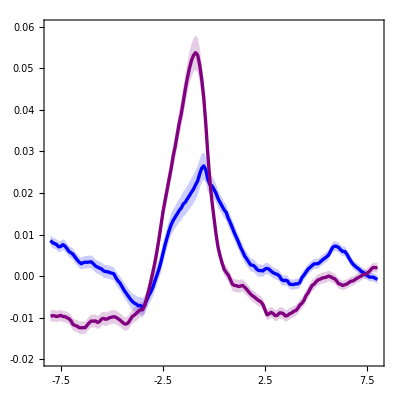

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFwhiskCCV1,Part[#,2]&/@meanDFFwhiskCCV1+(Part[#,2]&/@semDFFwhiskCCV1),Part[#,2]&/@meanDFFwhiskCCV1-(Part[#,2]&/@semDFFwhiskCCV1),Part[#,2]&/@meanDFFwhiskCCV2m,Part[#,2]&/@meanDFFwhiskCCV2m+(Part[#,2]&/@semDFFwhiskCCV2m),Part[#,2]&/@meanDFFwhiskCCV2m-(Part[#,2]&/@semDFFwhiskCCV2m)},Filling->{1->{{2},Directive[Opacity[0.2],Blue]},1->{{3},Directive[Opacity[0.2],Blue]},4->{{5},Directive[Opacity[0.2],Purple]},4->{{6},Directive[Opacity[0.2],Purple]}},PlotStyle->{{Blue,Thickness[0.006]},Transparent,Transparent,{Purple,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.02,0.06}},FrameTicks->{{LinTicks[-0.02,0.06,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(**********************************************)
(*******Generate plots in Figure S3D****************) 
(**********************************************)
```

```mathematica
meanDFFwhiskOnV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/meanDFFzTraceWhiskOnset_V2m.txt","List"];
```

```mathematica
semDFFwhiskOnV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/semDFFzTraceWhiskOnset_V2m.txt","List"];
```

```mathematica
(*********)
```

```mathematica
meanDFFwhiskOnV1=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/meanDFFzTraceWhiskOnset_V1.txt","List"];
```

```mathematica
semDFFwhiskOnV1=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/semDFFzTraceWhiskOnset_V1.txt","List"];
```

```mathematica
(*****************************)
```

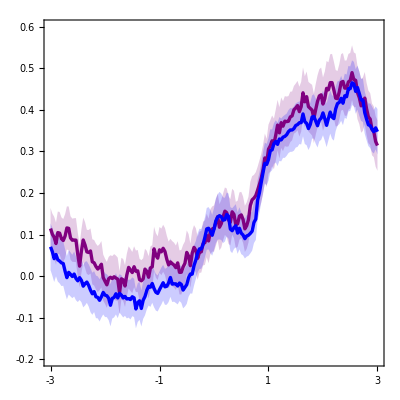

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFwhiskOnV2m,Part[#,2]&/@meanDFFwhiskOnV2m+(Part[#,2]&/@semDFFwhiskOnV2m),Part[#,2]&/@meanDFFwhiskOnV2m-(Part[#,2]&/@semDFFwhiskOnV2m),Part[#,2]&/@meanDFFwhiskOnV1,Part[#,2]&/@meanDFFwhiskOnV1+(Part[#,2]&/@semDFFwhiskOnV1),Part[#,2]&/@meanDFFwhiskOnV1-(Part[#,2]&/@semDFFwhiskOnV1)},Filling->{1->{{2},Directive[Opacity[0.2],v2mColor]},1->{{3},Directive[Opacity[0.2],v2mColor]},4->{{5},Directive[Opacity[0.2],v1Color]},4->{{6},Directive[Opacity[0.2],v1Color]}},PlotStyle->{{v2mColor,Thickness[0.006]},Transparent,Transparent,{v1Color,Thickness[0.006]},Transparent,Transparent},DataRange->{-3,3},PlotRange->{{-3,3},{-0.2,0.6}},FrameTicks->{{LinTicks[-0.2,0.6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-3,3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(**********************************************)
(*******Generate plots in Figure S3E****************) 
(**********************************************)
```

```mathematica
peakCCValsV1=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/peakDFFwhiskCC_V1.txt","List"];
```

```mathematica
peakCCValsV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/peakDFFwhiskCC_V2m.txt","List"];
```

```mathematica
v1Charts=Show[BoxWhiskerChart[peakCCValsV1,{{"Whiskers", Directive[Blue,Thick]}, {"Fences", Directive[Blue,Thick]},{"MedianMarker", Directive[Blue,Thickness[0.009]]}},PlotRange->{All,{-0.05,0.4}},ChartStyle->Directive[Blue,Opacity[0.3]],Frame->False],DistributionChart[peakCCValsV1,PlotRange->{All,{-0.05,0.4}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Blue],Frame->False],FrameTicks->{{LinTicks[-0.05,0.4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
pmCharts=Show[BoxWhiskerChart[peakCCValsV2m,{{"Whiskers", Directive[Purple,Thick]}, {"Fences", Directive[Purple,Thick]},{"MedianMarker", Directive[Purple,Thickness[0.009]]}},PlotRange->{All,{-0.05,0.4}},ChartStyle->Directive[Purple,Opacity[0.3]],Frame->False],DistributionChart[peakCCValsV2m,PlotRange->{All,{-0.05,0.4}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Purple],Frame->False],FrameTicks->{{LinTicks[-0.05,0.4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[peakCCValsV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{-0.05,0.4}},ChartStyle->Transparent,Frame->False],DistributionChart[peakCCValsV2m,PlotRange->{All,{-0.05,0.4}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[-0.05,0.4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

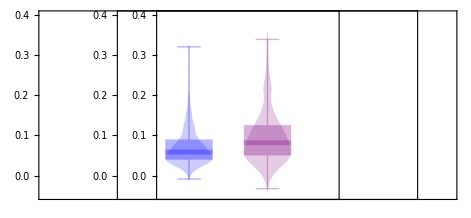

```mathematica
GraphicsRow[{v1Charts,pmCharts,transp},Spacings->{{-280,-280,-320}}]
```